```mathematica
f = Sqrt[1 + x] -1
```

-1+√(1+x)

```mathematica
pa = PadeApproximant[f,{x,0,{2,2}}]
```

(x/2+x^2/4)/(1+(3 x)/4+x^2/16)

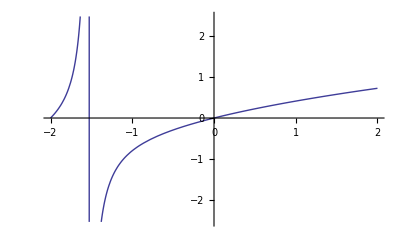

```mathematica
Plot[pa,{x,-2,2}]
```

```mathematica
g0 = Exp[I dz f]
```

ⅇ^(ⅈ dz (-1+√(1+x)))

```mathematica
pg = PadeApproximant[Exp[I  dz  f],{x,0,{2,2}}]
```

(1.+(0.6875+0.25 ⅈ) x+(0.0260417+0.109375 ⅈ) x^2)/(1.+(0.6875-0.25 ⅈ) x+(0.0260417-0.109375 ⅈ) x^2)

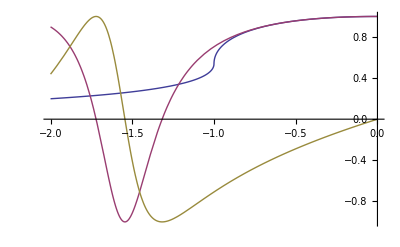

```mathematica
Plot[{Re[g0]/.dz->3.05,Re[pg]/.dz->3.05,Im[pg]/.dz->3.05},{x,-2,0}]
```

```mathematica
dz = 1.0;
```

```mathematica
tab = Table[{x,Re[g0],Im[g0],Re[pg],Im[pg]},{x,-2,0,0.001}];
```

```mathematica
OutputForm[TableForm[tab,TableSpacing->{0,2}]] >> pade_dz1-22.dat
```

```mathematica
pom = w'[x] + al (w'[x+dx] - 2 w'[x] + w'[x-dx]) - 1/(2 dx) ( w[x+dx] - w[x-dx])
```

-(-w[-dx+x]+w[dx+x])/(2 dx)+w'[x]+al (-2 w'[x]+w'[-dx+x]+w'[dx+x])

```mathematica
Series[pom,{dx,0,4}]
```

(-1/6 w^(3)[x]+al w^(3)[x]) dx^2+(-1/120 w^(5)[x]+1/12 al w^(5)[x]) dx^4+O[dx]^5

```mathematica
aux = w''[x] + al (w''[x+dx] - 2 w''[x] + w''[x-dx]) - 1/(dx^2) ( w[x+dx] -2 w[x] + w[x-dx])
```

-(-2 w[x]+w[-dx+x]+w[dx+x])/dx^2+w''[x]+al (-2 w''[x]+w''[-dx+x]+w''[dx+x])

```mathematica
Series[aux,{dx,0,4}]
```

(-1/12 w^(4)[x]+al w^(4)[x]) dx^2+(-1/360 w^(6)[x]+1/12 al w^(6)[x]) dx^4+O[dx]^5